```mathematica
a= x^2-40
```

x^2-40

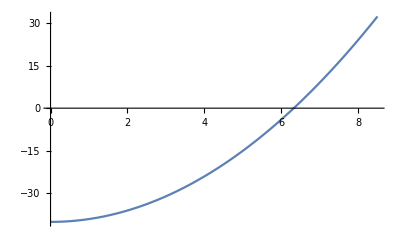

```mathematica
Plot[a,{x,0,8.5}]
```

```mathematica
Solve[a==0]
```

{{x→-2 √10},{x→2 √10}}

```mathematica
N[{{x->-2 √10},{x->2 √10}}]
```

{{x→-6.32456},{x→6.32456}}

```mathematica
Max[f[1]]
```

1

```mathematica
Integrate[f[x],{x,0,1}]
```

1/3

```mathematica
N[1/3]
```

0.333333

```mathematica
Solve[D[f[x]==0]]
```

{{x→0},{x→0}}

```mathematica
√(40^2+40^2)
```

40 √2

```mathematica
40^2
```

1600

```mathematica
.5*40*40
```

800.

```mathematica
b=s^2
c=40/(2 √10)s
```

s^2

2 √10 s

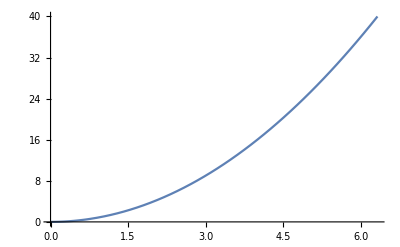

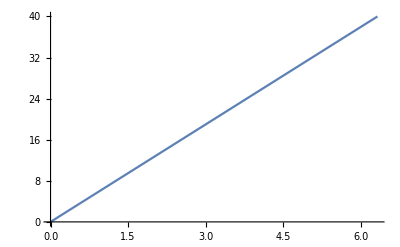

-Graphics--Graphics-

```mathematica
Curve=Plot[b,{s,0,2 √10}]
Line1=Plot[c,{s,0,2 √10}]
Overlay[ {Curve,Line1 } ]
```

```mathematica
Solve[b==c]
```

{{s→0},{s→2 √10}}

```mathematica
∫_0^a √(1+4 x^2)ⅆx
```

ConditionalExpression[1/4 (2 √(4 (x^2-40)^2+1) (x^2-40)+sinh^-1(2 (x^2-40))), -1/2<Im(x^2)<0∨0<Im(x^2)<1/2∨Re(x^2)≠40]

```mathematica
∫_0^(2 √10) √(1+4 x^2)ⅆx
```

√1610+1/4 sinh^-1(4 √10)

```mathematica
N[√1610+1/4 ArcSinh[4 √10]]
```

40.9329

```mathematica
Area1 = ∫_0^(2 √10) x^2 ⅆx
N[%]
Area2 = 0.5*40*2 √10
Area2-Area1
```

(80 √10)/3

84.3274

126.491

42.1637

```mathematica
D[t/x,x]
```

-t/x^2